```mathematica
Clear[a]
```

```mathematica
a=1;
```

```mathematica
H[qx_,qy_]:=({{2 Cos[qx a], Exp[-I qy a], 0, Exp[I qy a]}, {Exp[I qy a], -2 Sin[qx a], Exp[-I qy a], 0}, {0, Exp[I qy a], -2 Cos[qx a], Exp[-I qy a]}, {Exp[-I qy a], 0, Exp[I qy a], 2 Sin[qx a]}})
```

```mathematica
bands=Eigenvalues[H[qx,qy]]
```

{-ⅇ^(-ⅈ a qy) √(4 ⅇ^(2 ⅈ a qy)-√(1+12 ⅇ^(4 ⅈ a qy)+ⅇ^(8 ⅈ a qy)+2 ⅇ^(4 ⅈ a qy) Cos[4 a qx])),ⅇ^(-ⅈ a qy) √(4 ⅇ^(2 ⅈ a qy)-√(1+12 ⅇ^(4 ⅈ a qy)+ⅇ^(8 ⅈ a qy)+2 ⅇ^(4 ⅈ a qy) Cos[4 a qx])),-ⅇ^(-ⅈ a qy) √(4 ⅇ^(2 ⅈ a qy)+√(1+12 ⅇ^(4 ⅈ a qy)+ⅇ^(8 ⅈ a qy)+2 ⅇ^(4 ⅈ a qy) Cos[4 a qx])),ⅇ^(-ⅈ a qy) √(4 ⅇ^(2 ⅈ a qy)+√(1+12 ⅇ^(4 ⅈ a qy)+ⅇ^(8 ⅈ a qy)+2 ⅇ^(4 ⅈ a qy) Cos[4 a qx]))}

```mathematica
bands[[1]]//TeXForm//CopyToClipboard
```

```mathematica
bands[[2]]//TeXForm//CopyToClipboard
```

```mathematica
bands[[3]]//TeXForm//CopyToClipboard
```

```mathematica
bands[[4]]//TeXForm//CopyToClipboard
```

```mathematica
Series[bands[[1]], {qx,0,1},{qy,0,1}]//Simplify
```

(-(√2 √(a^2 qy^2) qy)/qy+O[qy]^2)+O[qx]^2

```mathematica
Series[bands[[2]], {qx,0,1},{qy,0,1}]//Simplify
```

((√2 √(a^2 qy^2) qy)/qy+O[qy]^2)+O[qx]^2

```mathematica
Series[bands[[3]], {qx,0,1},{qy,0,1}]//Simplify
```

(-2 √2+O[qy]^2)+O[qx]^2

```mathematica
Series[bands[[4]], {qx,0,1},{qy,0,1}]//Simplify
```

(2 √2+O[qy]^2)+O[qx]^2

```mathematica
eivals=Transpose[Table[Eigenvalues[H[kx,0]],{kx,0,Pi,0.01}]];
```

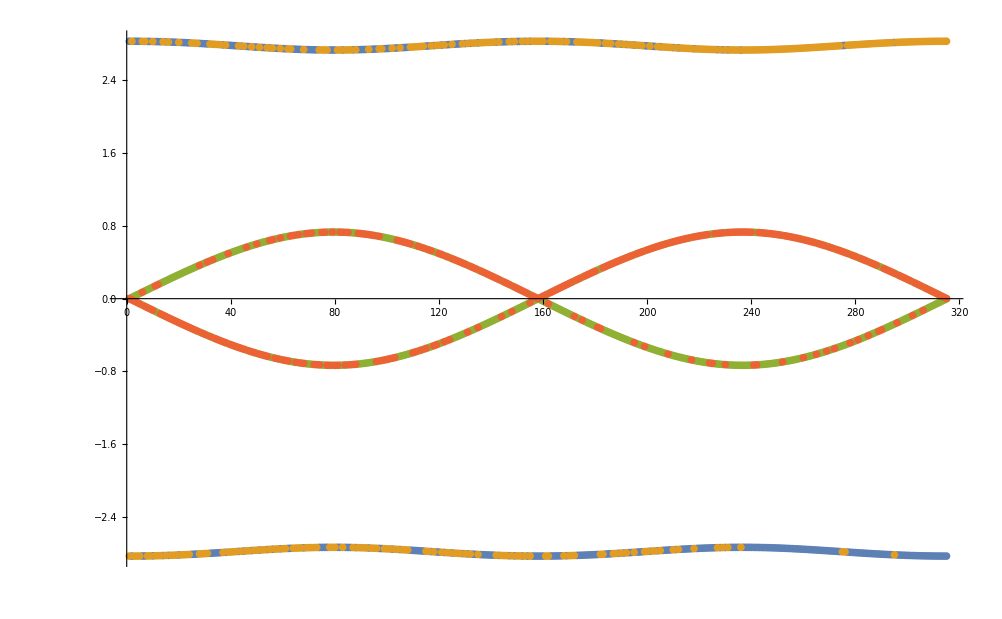

```mathematica
ListPlot[eivals]
```